## Scalar Green function in AdS_3 Vaidya

#### Order in future time upto which the Green function is evaluated

```mathematica
i=56;
```

### Input parameters and assumptions

t = -t_1, and t_1< 0 is the past time, used in the text.

```mathematica
t=1.7;
ν=0.667;
k=1.571;
```

```mathematica
$Assumptions=And[z∈Reals,z≥0,z≤1,ω∈Reals];
```

### Series expansion of the coefficient of z^(Δ_+)of the v < 0 solution,

lstJ lists the (J̃)_n

```mathematica
lstJ=CoefficientList[Series[(k Sqrt[t^2+2 t z])^(-ν-1/2) BesselJ[-ν-1/2,k Sqrt[t^2+2 t z]],{z,0,1}],z];
Do[AppendTo[lstJ,-((2 (l-1) (l+ν-1/2) lstJ[[l]]+k^2 t lstJ[[l-1]])/(t l (l-1)))],{l,2,i}];
```

### Series expansion of the coefficient of z^(Δ_+)of the v > 0 solution,

a[ n ] are arrays which list a_n^j

```mathematica
H[z_]=Series[(1+z)^(-I ω) Hypergeometric2F1[1/2 (1+ν-I (ω+k)),1/2 (1+ν-I (ω-k)),1+ν,z^2],{z,0,i}];
lstH=CoefficientList[H[z],z];
For[n=0,n≤i,n++,a[n]=CoefficientList[lstH[[n+1]],ω]];
```

### Moments, M, are calculated using eq. (2.14) and (2.15)

```mathematica
M=ConstantArray[lstJ[[1]],1];
For[j=2,j≤i+1,j++,AppendTo[M,1/a[j-1][[j]] (lstJ[[j]]-Sum[M[[l]] a[j-1][[l]],{l,1,j-1}])];
If[EvenQ[j],M[[j]]=M[[j]]-Re[M[[j]]],M[[j]]=M[[j]]-I Im[M[[j]]]]];
```

### The thermalizing Green function of eq. (2.18) is constructed and Pade Approximation is used

```mathematica
G[x_]=-2 ν 2^(-ν+1/2) Sqrt[π]/Gamma[ν] k^(2 (ν+1/2)) PadeApproximant[Sum[(-I x)^l/l! M[[l+1]],{l,0,i}],{x,0,{i/2-1,i/2+1}}];
```

### Vacuum Green function

```mathematica
Gvac[x_]=-2 ν 2^(-ν+1/2) Sqrt[π]/Gamma[ν] (k/(x+t))^(ν+1/2) BesselJ[-ν-1/2,k (x+t)];
```

### The thermal Green function of eq. (B.2)

```mathematica
Clear[n];
Δ=1+ν;
ω[n_,a_,k_]=a k-I (Δ+2 n);
Gtherm[v_]=1/(2 Sin[π Δ] Gamma[Δ]^2)Sum[Sum[(-1)^n/n! Exp[-I ω[n,a,k] (v+t)] Gamma[Δ/2+I/2 (ω[n,a,k]-a k)]Gamma[Δ/2+I/2 (ω[n,a,k]+a k)] Gamma[Δ/2-I/2 (ω[n,a,k]+a k)](Cos[π Δ] Cosh[π ω[n,a,k]]-Cosh[π k]-I Sin[π Δ] Sinh[π ω[n,a,k]]),{n,0,100,1}],{a,-1,1,2}];
```

### Plots of figures 2 and 3

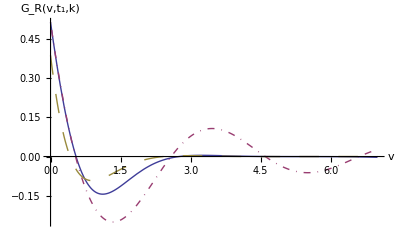

```mathematica
Plot[{G[x],Gvac[x],Gtherm[x]},{x,0,7},PlotStyle->{{Thick,Dashing[None]},{Thick,DotDashed},{Thick,Dashing[Large]}},PlotRange->Full,AxesLabel->{Style["v",FontSize->16],Style["\!\(\*SubscriptBox[\(G\), \(R\)]\)(v,\!\(\*SubscriptBox[\(t\), \(1\)]\),k)",FontSize->16]}]
```

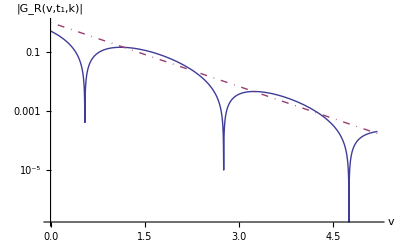

```mathematica
LogPlot[{Abs[G[v]],Exp[-(1+ν) v]},{v,0,5.2},PlotStyle->{Thick,{Thick,DotDashed}},AxesLabel->{Style["v",FontSize->16],Style["|\!\(\*SubscriptBox[\(G\), \(R\)]\)(v,\!\(\*SubscriptBox[\(t\), \(1\)]\),k)|",FontSize->16]}]
```